```mathematica
Needs["Quantum`"]
```

## Definitions

```mathematica
EigenvaluesFromTaus[taus_List]:=Eigenvalues[JamiolkowskiOperatorChoiToState[PauliSuperoperator[taus]]]

EigenvalSigns1QubitPCE[]:={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
EigenSignsPCE[n_Integer]:=Nest[KroneckerProduct[EigenvalSigns1QubitPCE[],#]&,EigenvalSigns1QubitPCE[],n-1]
```

```mathematica
Subscript[τ, 0]=1;τ1q=Table[Subscript[τ, i],{i,0,3}]
```

{1,τ_1,τ_2,τ_3}

```mathematica
Subscript[τ, 0,0]=1;τ2q=Table[Subscript[τ, i,j],{i,0,3},{j,0,3}]//Flatten
```

{1,τ_(0,1),τ_(0,2),τ_(0,3),τ_(1,0),τ_(1,1),τ_(1,2),τ_(1,3),τ_(2,0),τ_(2,1),τ_(2,2),τ_(2,3),τ_(3,0),τ_(3,1),τ_(3,2),τ_(3,3)}

## Trying

```mathematica
EigenvaluesFromTaus[Table[Subscript[τ, i]^a,{i,0,3}]]//Total//FullSimplify
```

1

```mathematica
Pauli[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
KroneckerProduct[EigenvaluesFromTaus[Table[Subscript[τ, i]^a,{i,0,3}]],EigenvaluesFromTaus[Table[Subscript[τ, i]^b,{i,0,3}]]]
```

{{1/16 (1+τ_1^a-τ_2^a-τ_3^a) (1+τ_1^b-τ_2^b-τ_3^b),1/16 (1+τ_1^a-τ_2^a-τ_3^a) (1-τ_1^b-τ_2^b+τ_3^b),1/16 (1+τ_1^a-τ_2^a-τ_3^a) (1-τ_1^b+τ_2^b-τ_3^b),1/16 (1+τ_1^a-τ_2^a-τ_3^a) (1+τ_1^b+τ_2^b+τ_3^b)},{1/16 (1-τ_1^a-τ_2^a+τ_3^a) (1+τ_1^b-τ_2^b-τ_3^b),1/16 (1-τ_1^a-τ_2^a+τ_3^a) (1-τ_1^b-τ_2^b+τ_3^b),1/16 (1-τ_1^a-τ_2^a+τ_3^a) (1-τ_1^b+τ_2^b-τ_3^b),1/16 (1-τ_1^a-τ_2^a+τ_3^a) (1+τ_1^b+τ_2^b+τ_3^b)},{1/16 (1-τ_1^a+τ_2^a-τ_3^a) (1+τ_1^b-τ_2^b-τ_3^b),1/16 (1-τ_1^a+τ_2^a-τ_3^a) (1-τ_1^b-τ_2^b+τ_3^b),1/16 (1-τ_1^a+τ_2^a-τ_3^a) (1-τ_1^b+τ_2^b-τ_3^b),1/16 (1-τ_1^a+τ_2^a-τ_3^a) (1+τ_1^b+τ_2^b+τ_3^b)},{1/16 (1+τ_1^a+τ_2^a+τ_3^a) (1+τ_1^b-τ_2^b-τ_3^b),1/16 (1+τ_1^a+τ_2^a+τ_3^a) (1-τ_1^b-τ_2^b+τ_3^b),1/16 (1+τ_1^a+τ_2^a+τ_3^a) (1-τ_1^b+τ_2^b-τ_3^b),1/16 (1+τ_1^a+τ_2^a+τ_3^a) (1+τ_1^b+τ_2^b+τ_3^b)}}

```mathematica
eig1Q=EigenvaluesFromTaus[Table[Subscript[τ, i],{i,0,3}]];MatrixForm/@Table[eig1Q[[i+1]]Pauli[i],{i,0,3}]
```

{(1/4 (1+τ_1-τ_2-τ_3) | 0
0 | 1/4 (1+τ_1-τ_2-τ_3)),(0 | 1/4 (1-τ_1-τ_2+τ_3)
1/4 (1-τ_1-τ_2+τ_3) | 0),(0 | -1/4 ⅈ (1-τ_1+τ_2-τ_3)
1/4 ⅈ (1-τ_1+τ_2-τ_3) | 0),(1/4 (1+τ_1+τ_2+τ_3) | 0
0 | 1/4 (-1-τ_1-τ_2-τ_3))}

```mathematica
s=Table[Outer[Times,Flatten[Pauli[i]],Flatten[Pauli[i]]],{i,0,3}]
```

{{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}},{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}},{{0,0,0,0},{0,-1,1,0},{0,1,-1,0},{0,0,0,0}},{{1,0,0,-1},{0,0,0,0},{0,0,0,0},{-1,0,0,1}}}

```mathematica
MatrixForm/@{s[[1]]+s[[2]]+s[[3]]+s[[4]],s[[1]]+s[[2]]-s[[3]]-s[[4]],s[[1]]-s[[2]]+s[[3]]-s[[4]],s[[1]]-s[[2]]-s[[3]]+s[[4]]}
```

{(2 | 0 | 0 | 0
0 | 0 | 2 | 0
0 | 2 | 0 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 2
0 | 2 | 0 | 0
0 | 0 | 2 | 0
2 | 0 | 0 | 0),(0 | 0 | 0 | 2
0 | -2 | 0 | 0
0 | 0 | -2 | 0
2 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 0 | -2 | 0
0 | -2 | 0 | 0
0 | 0 | 0 | 2)}

#### Parece que era importante escoger adecuadamente el orden de los coeficientes a_(j_1,…,j_n)^(μ_1,…,μ_n)de los τ_(j_1,…,j_n)de los eigenvalores:

```mathematica
Table[HermitianMatrixQ[EigenSignsPCE[i]],{i,7}]
```

{True,True,True,True,True,True,True}

#### Para 2 qubits

```mathematica
EigenSignsPCE[2].ReplacePart[#,Position[#,-1]->0]&/@EigenSignsPCE[2]
```

{{16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,0,0,8,0,0,0,0,0,0,0,0,0,0,0,0},{8,0,0,0,8,0,0,0,0,0,0,0,0,0,0,0},{8,0,0,0,0,8,0,0,0,0,0,0,0,0,0,0},{8,0,0,0,0,0,8,0,0,0,0,0,0,0,0,0},{8,0,0,0,0,0,0,8,0,0,0,0,0,0,0,0},{8,0,0,0,0,0,0,0,8,0,0,0,0,0,0,0},{8,0,0,0,0,0,0,0,0,8,0,0,0,0,0,0},{8,0,0,0,0,0,0,0,0,0,8,0,0,0,0,0},{8,0,0,0,0,0,0,0,0,0,0,8,0,0,0,0},{8,0,0,0,0,0,0,0,0,0,0,0,8,0,0,0},{8,0,0,0,0,0,0,0,0,0,0,0,0,8,0,0},{8,0,0,0,0,0,0,0,0,0,0,0,0,0,8,0},{8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8}}

```mathematica
ReplacePart[#,Position[#,-1]->0]&/@EigenSignsPCE[2]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1}}

```mathematica
(ReplacePart[#,Position[#,-1]->0]&/@EigenSignsPCE[2])[[2;;]]==(1/2EigenSignsPCE[2].{1}~Join~#&/@DiagonalMatrix[ConstantArray[1,15]])
```

True

{2,0,2,0}

Inequalities that need to be satisfied for 2 qubits may be written as 
				a_(j_1, j_2)^(μ_1, μ_2)τ_(j_1,j_2)=τ'_(j_1,j_2),
where τ_(j_1,j_2)define a PCE quantum channel if τ'_(j_1,j_2)≥0.

#### Matrix a_(j_1, j_2)^(μ_1, μ_2) for 2 qubits:

```mathematica
EigenSignsPCE[1]
```

{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}}

```mathematica
EigenSignsPCE[2].{1,1,1,1,0}~Join~ConstantArray[0,11]
```

{4,0,0,0,4,0,0,0,4,0,0,0,4,0,0,0}

```mathematica
EigenSignsPCE[2]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1)

El número de + y - en cada

```mathematica
componentsInvariant=2;
ArrayReshape[Total[#]&/@Flatten[Partition[#,componentsInvariant]&/@EigenSignsPCE[3],1],{64,64/componentsInvariant}]
```

```mathematica
2^(2*2-1)
```

8

```mathematica
n=2;componentsInvariant=8;
ArrayReshape[Count[#,1]&/@Flatten[Partition[#,componentsInvariant]&/@EigenSignsPCE[n],1],{4^n,(4^n/componentsInvariant)}]
```

{{8,8},{4,4},{4,4},{4,4},{8,0},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4}}

¿Qué restricción impone ese {8,-8}? 

8 positivos, 8 negativos.

```mathematica
EigenSignsPCE[2].Flatten[Normal[SparseArray[{{1,1},{3,4},{3,3},{4,2},{3,2},{4,1}}->{1,1,1,1,1,1},{4,4}]]]
```

{6,2,0,0,-4,0,2,2,2,-2,0,0,0,4,2,2}

```mathematica
arr=Flatten[Normal[SparseArray[{{1,1},{1,3},{2,1},{2,3}}->{1,1,1,1},{4,4}]]];
EigenSignsPCE[2].arr
PCEFigures/@ArrayReshape[{#,1/4EigenSignsPCE[2].#},{2,4,4}]&[#]&[arr]
```

{4,0,4,0,4,0,4,0,0,0,0,0,0,0,0,0}

{-Graphics-,-Graphics-}

```mathematica
twoQubits2InvComp={1}~Join~#&/@DiagonalMatrix[ConstantArray[1,15]];
```

```mathematica
(PCEFigures/@ArrayReshape[{#,1/2EigenSignsPCE[2].#},{2,4,4}]&[#])&/@twoQubits2InvComp//Transpose//GraphicsGrid
```

-Graphics-

#### Parece que esto está asociando a un canal con otro del otro lado del arcoiris O.o

#### Goal: find a proof that choosing the positive τ_(j_1,…,j_n)as the components left invariant and the negative τ_(j_1,…,j_n)as the components erased in every eigenvalue λ_(j_1,…,j_n) the PCE operation is CP, i.e. every λ_(j_1,…,j_n)≥0.

#### La elección de a_(j_1, j_2)^(μ_1, μ_2)=-1 →0 hace que λ_(0,0),λ_(l,m)>0. Ambos desigualdades se cumplen trivialmente ya que sólo sobreviven τ_(j_1,j_2) positivos. El resto de eigenvalores se hace cero, ¿prueba?.

```mathematica
1/16ReplacePart[EigenSignsPCE[2],{_}~Join~#&/@Position[EigenSignsPCE[2][[#]],-1]->0].Normal[SparseArray[{1,#}->{1,1},16]]&/@Range[16]
```

{{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16},{1/8,1/8,0,0,1/8,1/8,0,0,1/8,1/8,0,0,1/8,1/8,0,0},{1/8,0,1/8,0,1/8,0,1/8,0,1/8,0,1/8,0,1/8,0,1/8,0},{1/8,0,0,1/8,1/8,0,0,1/8,1/8,0,0,1/8,1/8,0,0,1/8},{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0},{1/8,1/8,0,0,1/8,1/8,0,0,0,0,1/8,1/8,0,0,1/8,1/8},{1/8,0,1/8,0,1/8,0,1/8,0,0,1/8,0,1/8,0,1/8,0,1/8},{1/8,0,0,1/8,1/8,0,0,1/8,0,1/8,1/8,0,0,1/8,1/8,0},{1/8,1/8,1/8,1/8,0,0,0,0,1/8,1/8,1/8,1/8,0,0,0,0},{1/8,1/8,0,0,0,0,1/8,1/8,1/8,1/8,0,0,0,0,1/8,1/8},{1/8,0,1/8,0,0,1/8,0,1/8,1/8,0,1/8,0,0,1/8,0,1/8},{1/8,0,0,1/8,0,1/8,1/8,0,1/8,0,0,1/8,0,1/8,1/8,0},{1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0,1/8,1/8,1/8,1/8},{1/8,1/8,0,0,0,0,1/8,1/8,0,0,1/8,1/8,1/8,1/8,0,0},{1/8,0,1/8,0,0,1/8,0,1/8,0,1/8,0,1/8,1/8,0,1/8,0},{1/8,0,0,1/8,0,1/8,1/8,0,0,1/8,1/8,0,1/8,0,0,1/8}}

```mathematica
16(EigenSignsPCE[2]//Inverse)//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1)

```mathematica
taus=Inverse[EigenSignsPCE[2]].Flatten[Table[Subscript[λ, i,j],{i,0,3},{j,0,3}]]//Factor
```

{1/16 (λ_(0,0)+λ_(0,1)+λ_(0,2)+λ_(0,3)+λ_(1,0)+λ_(1,1)+λ_(1,2)+λ_(1,3)+λ_(2,0)+λ_(2,1)+λ_(2,2)+λ_(2,3)+λ_(3,0)+λ_(3,1)+λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)-λ_(0,2)-λ_(0,3)+λ_(1,0)+λ_(1,1)-λ_(1,2)-λ_(1,3)+λ_(2,0)+λ_(2,1)-λ_(2,2)-λ_(2,3)+λ_(3,0)+λ_(3,1)-λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)+λ_(0,2)-λ_(0,3)+λ_(1,0)-λ_(1,1)+λ_(1,2)-λ_(1,3)+λ_(2,0)-λ_(2,1)+λ_(2,2)-λ_(2,3)+λ_(3,0)-λ_(3,1)+λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)-λ_(0,2)+λ_(0,3)+λ_(1,0)-λ_(1,1)-λ_(1,2)+λ_(1,3)+λ_(2,0)-λ_(2,1)-λ_(2,2)+λ_(2,3)+λ_(3,0)-λ_(3,1)-λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)+λ_(0,2)+λ_(0,3)+λ_(1,0)+λ_(1,1)+λ_(1,2)+λ_(1,3)-λ_(2,0)-λ_(2,1)-λ_(2,2)-λ_(2,3)-λ_(3,0)-λ_(3,1)-λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)-λ_(0,2)-λ_(0,3)+λ_(1,0)+λ_(1,1)-λ_(1,2)-λ_(1,3)-λ_(2,0)-λ_(2,1)+λ_(2,2)+λ_(2,3)-λ_(3,0)-λ_(3,1)+λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)+λ_(0,2)-λ_(0,3)+λ_(1,0)-λ_(1,1)+λ_(1,2)-λ_(1,3)-λ_(2,0)+λ_(2,1)-λ_(2,2)+λ_(2,3)-λ_(3,0)+λ_(3,1)-λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)-λ_(0,2)+λ_(0,3)+λ_(1,0)-λ_(1,1)-λ_(1,2)+λ_(1,3)-λ_(2,0)+λ_(2,1)+λ_(2,2)-λ_(2,3)-λ_(3,0)+λ_(3,1)+λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)+λ_(0,2)+λ_(0,3)-λ_(1,0)-λ_(1,1)-λ_(1,2)-λ_(1,3)+λ_(2,0)+λ_(2,1)+λ_(2,2)+λ_(2,3)-λ_(3,0)-λ_(3,1)-λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)-λ_(0,2)-λ_(0,3)-λ_(1,0)-λ_(1,1)+λ_(1,2)+λ_(1,3)+λ_(2,0)+λ_(2,1)-λ_(2,2)-λ_(2,3)-λ_(3,0)-λ_(3,1)+λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)+λ_(0,2)-λ_(0,3)-λ_(1,0)+λ_(1,1)-λ_(1,2)+λ_(1,3)+λ_(2,0)-λ_(2,1)+λ_(2,2)-λ_(2,3)-λ_(3,0)+λ_(3,1)-λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)-λ_(0,2)+λ_(0,3)-λ_(1,0)+λ_(1,1)+λ_(1,2)-λ_(1,3)+λ_(2,0)-λ_(2,1)-λ_(2,2)+λ_(2,3)-λ_(3,0)+λ_(3,1)+λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)+λ_(0,2)+λ_(0,3)-λ_(1,0)-λ_(1,1)-λ_(1,2)-λ_(1,3)-λ_(2,0)-λ_(2,1)-λ_(2,2)-λ_(2,3)+λ_(3,0)+λ_(3,1)+λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)-λ_(0,2)-λ_(0,3)-λ_(1,0)-λ_(1,1)+λ_(1,2)+λ_(1,3)-λ_(2,0)-λ_(2,1)+λ_(2,2)+λ_(2,3)+λ_(3,0)+λ_(3,1)-λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)+λ_(0,2)-λ_(0,3)-λ_(1,0)+λ_(1,1)-λ_(1,2)+λ_(1,3)-λ_(2,0)+λ_(2,1)-λ_(2,2)+λ_(2,3)+λ_(3,0)-λ_(3,1)+λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)-λ_(0,2)+λ_(0,3)-λ_(1,0)+λ_(1,1)+λ_(1,2)-λ_(1,3)-λ_(2,0)+λ_(2,1)+λ_(2,2)-λ_(2,3)+λ_(3,0)-λ_(3,1)-λ_(3,2)+λ_(3,3))}

```mathematica
taus[[1;;4]]
```

{1/16 (λ_(0,0)+λ_(0,1)+λ_(0,2)+λ_(0,3)+λ_(1,0)+λ_(1,1)+λ_(1,2)+λ_(1,3)+λ_(2,0)+λ_(2,1)+λ_(2,2)+λ_(2,3)+λ_(3,0)+λ_(3,1)+λ_(3,2)+λ_(3,3)),1/16 (λ_(0,0)+λ_(0,1)-λ_(0,2)-λ_(0,3)+λ_(1,0)+λ_(1,1)-λ_(1,2)-λ_(1,3)+λ_(2,0)+λ_(2,1)-λ_(2,2)-λ_(2,3)+λ_(3,0)+λ_(3,1)-λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)+λ_(0,2)-λ_(0,3)+λ_(1,0)-λ_(1,1)+λ_(1,2)-λ_(1,3)+λ_(2,0)-λ_(2,1)+λ_(2,2)-λ_(2,3)+λ_(3,0)-λ_(3,1)+λ_(3,2)-λ_(3,3)),1/16 (λ_(0,0)-λ_(0,1)-λ_(0,2)+λ_(0,3)+λ_(1,0)-λ_(1,1)-λ_(1,2)+λ_(1,3)+λ_(2,0)-λ_(2,1)-λ_(2,2)+λ_(2,3)+λ_(3,0)-λ_(3,1)-λ_(3,2)+λ_(3,3))}

```mathematica
Total[lambdas[[2;;]]]-lambdas[[3]]//FullSimplify
```

1/8 (7 τ_(0,0)-τ_(0,2)-τ_(1,0)-τ_(1,2)-τ_(2,0)-τ_(2,2)-τ_(3,0)-τ_(3,2))

```mathematica
Eigenvalues[EigenSignsPCE[2]]
```

{-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,4,4,4,4}

```mathematica
PCEFigures@Normal[SparseArray[{{1,1},{1,4},{2,1}}->{1,1,1},{4,4}]]
```

-Graphics-

```mathematica
lambdas=EigenvaluesFromTaus[{1,1,1}~Join~ConstantArray[0,13]]
```

{3/16,3/16,3/16,3/16,-1/16,-1/16,-1/16,-1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

```mathematica
BadIndicesFromTaus[tau_List]:=IntegerDigits[#-1,4,2]&/@Flatten[Position[EigenvaluesFromTaus[tau],x_/;x<0]]
```

```mathematica
tau={1,1,1}~Join~ConstantArray[0,13];
PCEFigures@ArrayReshape[tau,{4,4}]
EigenvaluesFromTaus[tau]
```

-Graphics-

{3/16,3/16,3/16,3/16,-1/16,-1/16,-1/16,-1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

### 3 componentes invariantes:

```mathematica
BadIndicesFromTaus@Normal[SparseArray[#->{1,1,1},16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{2}])
```

### 5 componentes invariantes:

```mathematica
i=5;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,2},{0,3}}
{{0,1},{1,2},{1,3},{2,0},{2,1}}
{{1,0},{1,1},{1,2},{1,3},{2,0},{2,1}})

### 6 componentes invariantes:

```mathematica
i=6;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1},{0,3}}
{{0,2},{0,3}}
{{0,3},{1,0},{1,1}}
{{0,1},{0,2},{0,3},{1,0},{1,1}})

```mathematica
i=7;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1},{1,1},{1,2},{1,3}}
{{0,1},{0,2},{1,3},{2,0},{2,1}}
{{0,2},{0,3},{1,0},{1,1},{1,2},{1,3}}
{{0,2},{1,1},{1,2},{1,3},{2,0},{2,1}}
{{1,3},{2,0},{2,1},{2,2},{2,3},{3,0},{3,1},{3,2},{3,3}})

```mathematica
i=9;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1}}
{{0,2},{0,3},{1,0}}
{{0,1},{1,1},{1,2},{1,3},{2,0}}
{{0,1},{0,2},{1,3},{2,0},{2,1},{2,2}}
{{0,2},{0,3},{1,0},{1,1},{1,2},{1,3},{2,0}}
{{0,2},{1,1},{1,2},{1,3},{2,0},{2,1},{2,2}})

```mathematica
i=10;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1}}
{{0,1},{0,3},{1,0}}
{{0,2},{0,3},{1,0}}
{{0,3},{1,0},{1,1},{1,2}}
{{0,1},{0,2},{0,3},{1,0},{1,1},{1,2}})

```mathematica
i=11;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1},{1,0},{1,1},{1,2},{1,3}}
{{0,1},{0,2},{1,2},{1,3},{2,0},{2,1}}
{{0,2},{1,0},{1,1},{1,2},{1,3},{2,0},{2,1}}
{{1,2},{1,3},{2,0},{2,1},{2,2},{2,3},{3,0},{3,1},{3,2},{3,3}})

```mathematica
i=12;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1}}
{{0,1},{0,2},{0,3}}
{{0,2},{0,3},{1,0},{1,1}})

```mathematica
i=13;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

({{0,1},{0,2},{0,3}}
{{0,1},{1,0},{1,1},{1,2},{1,3},{2,0},{2,1}})

```mathematica
i=14;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

((0
1) | (0
2) | (0
3))

```mathematica
i=15;
Union[BadIndicesFromTaus@Normal[SparseArray[#->ConstantArray[1,i],16]]&/@({1}~Join~#&/@Subsets[Range[15]+1,{i-1}])]//MatrixForm
```

((0
1) | (0
2) | (0
3) | (1
0) | (1
1) | (1
2) | (1
3))

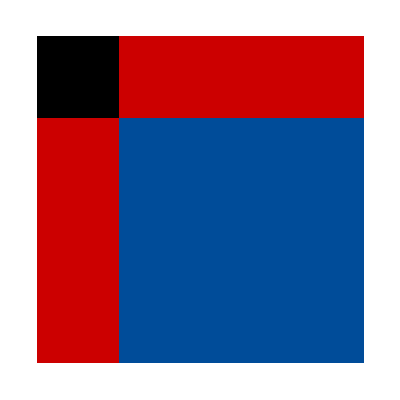
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PCEFigures/@ArrayReshape[EigenSignsPCE[2],{16,4,4}]
```

```mathematica
EigenvaluesFromTaus[Table[Subscript[τ, i,j],{i,0,3},{j,0,3}]]
```

{1/16 (τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3)),1/16 (τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3))}

Φτ=λ
τ=Φ^-1λ

#### Para encontrar μ_1,μ_2 para los cuales λ_(μ_1,μ_2)<0:

```mathematica
EigenvaloresNegativos[i_]:=Module[{τ},
τ=Normal[SparseArray[{1}~Join~#->ConstantArray[1,i],16]]&/@Subsets[Range[2,16],{i-1}];
IntegerDigits[#-1,4,2]&/@(Flatten[Position[EigenSignsPCE[2].#,x_/;x<0]]&/@τ)
]
```

#### Tabla con la cantidad de λ_(μ_1,μ_2)<0 según la cantidad de configuraciones de τ⃗ por número de τ_(j_1,j_2) invariantes

```mathematica
Table[TableForm[{{ToString[Style[i,Bold]]<>" τ_j_1 invariantes:"},{"λ_(μ_1,μ_2)<0","Configuraciones de τ⃗","Configuraciones únicas de τ⃗"}}~Join~Join[Sort[Tally[Length[#]&/@EigenvaloresNegativos[i]]],Transpose[{Sort[Tally[Length[#]&/@Union[EigenvaloresNegativos[i]]]]}[[;;,;;,2]]],2]~Join~{{}},TableAlignments->Center],{i,16}]//TableForm
```

1 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
0 | 1 | 1
 |  | 
2 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
0 | 15 | 1
 |  | 
3 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
4 | 105 | 105
 |  | 
4 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
0 | 35 | 1
2 | 420 | 105
 |  | 
5 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
2 | 105 | 105
5 | 840 | 168
6 | 420 | 420
 |  | 
6 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
2 | 1155 | 105
3 | 1680 | 420
5 | 168 | 168
 |  | 
7 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
4 | 420 | 420
5 | 1680 | 168
6 | 2625 | 2625
9 | 280 | 280
 |  | 
8 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
0 | 15 | 1
1 | 540 | 15
3 | 3360 | 420
4 | 2520 | 840
 |  | 
9 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
1 | 15 | 15
3 | 420 | 420
5 | 840 | 840
6 | 2520 | 280
7 | 2640 | 2640
 |  | 
10 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
1 | 105 | 15
3 | 2940 | 420
4 | 1680 | 420
6 | 280 | 280
 |  | 
11 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
5 | 315 | 315
6 | 1680 | 280
7 | 840 | 840
10 | 168 | 168
 |  | 
12 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
1 | 105 | 15
3 | 420 | 35
4 | 840 | 840
 |  | 
13 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
3 | 35 | 35
7 | 420 | 420
 |  | 
14 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
3 | 105 | 35
 |  | 
15 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
7 | 15 | 15
 |  | 
16 τ_j_1 invariantes: |  | 
λ_(μ_1,μ_2)<0 | Configuraciones de τ⃗ | Configuraciones únicas de τ⃗
0 | 1 | 1
 |  |

#### Cuenta de a’s = +1

```mathematica
Count[#,1]&/@Partition[#,4]&/@EigenSignsPCE[2]//MatrixForm
```

(4 | 4 | 4 | 4
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
4 | 4 | 0 | 0
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
4 | 0 | 4 | 0
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
4 | 0 | 0 | 4
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2)

#### There is an interesting pattern in every partition of four columns, could it be exploited?

```mathematica
MatrixForm/@Table[EigenSignsPCE[2][[;;,i+1;;i+4]],{i,0,15,4}]
```

{(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1),(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1),(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1),(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1
-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1
1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)}

```mathematica
Partition[EigenSignsPCE[2],{4,4}]//MatrixForm
```

((1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)
(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1)
(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1)
(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1) | (-1 | -1 | -1 | -1
-1 | -1 | 1 | 1
-1 | 1 | -1 | 1
-1 | 1 | 1 | -1) | (1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1))

9 am o 4 pm, viernes